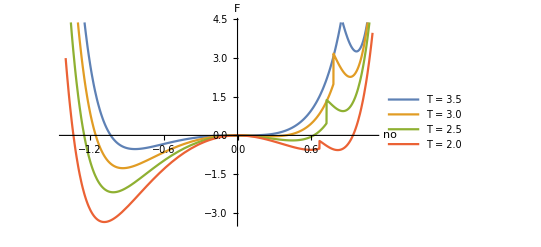

fid.png

```mathematica
FvdW=τ (no+1) Log[((no+1) (1-b))/(1-(no+1) b)]-a1 no^2-(τ no)/(1-b);
FvdWexpansion=Normal[Series[FvdW,{no,0,10}]];
Fex=-Bx τ Exp[-τ/Tm] 3 ϕ^2+(d no^2)/2;
Fzeta1=1/2 a2 (6 ϕ^2);
Fzeta2=1/3 a3 (18 no ϕ^2+12 ϕ^3);
Fzeta3=1/4 a4 (36 no^2 ϕ^2+48 no ϕ^3+90 ϕ^4);
F=FvdWexpansion+Fex+Fzeta1+Fzeta2+Fzeta3;
nmin=-1.4;
nmax=1.1;
(*Fsubs=F/.{a1->7.3,b->0.5,a2->-1.8+2.38 τ+0.05 τ^2,a3->0.56-1.085 τ+0.066 τ^2,a4->0.096,Bx->1.5,Tm->1.2,d->0.2};*)
Fsubs=F/.{a1->7.3,b->0.5,a2->-1.8+2.38 τ+0.05 τ^2,a3->0.56-1.085 τ+0.066 τ^2,a4->0.096,Bx->1.5,Tm->1.2,d->0.2};
Ffcc[n0_,T_]:=FindMinimum[{Fsubs/.{no->n0,τ->T},{ϕ}∈Reals,ϕ≥0},{ϕ,1.0}]⟦1⟧;
Fl[n0_,T_]:=Fsubs/.{ϕ->0,no->n0,τ->T};
plottingT=1.6;
p1=Show[Plot[{Ffcc[nn,3.5],Ffcc[nn,3.0],Ffcc[nn,2.5],Ffcc[nn,2.0]},{nn,nmin,nmax},PlotLegends->{"T = 3.5","T = 3.0","T = 2.5","T = 2.0"},AxesLabel->{"no","F"}]]
Export["fid.png",p1]
```

0.005

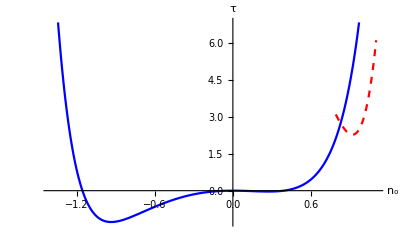

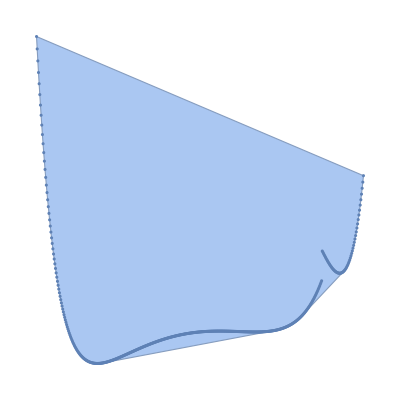

Show::gtype: Symbol is not a type of graphics.

```mathematica
nStep = 0.005
plottingT = 3.0;
pa = Plot[Fl[nn, plottingT], {nn, nmin, nmax}, PlotStyle->{ Blue},AxesLabel->{Style["n_o",Black, FontSize->15], Style["τ",Black, FontSize-> 15]}];
pb = Plot[Ffcc[nn, plottingT], {nn, 0.79, nmax}, PlotStyle-> {Red, Dashed}];
Show[pa, pb]

fcn=Table[{i,Ffcc[i, plottingT]},{i,nmin,nmax,nStep}]  ;
convHull = ConvexHullMesh[fcn];
Show[convHull,ListPlot[fcn],AspectRatio->1]
```

```mathematica
commonTangent = {};
convexStep = 0.0025;
fcn=Table[{i,Ffcc[i, plottingT]},{i,nmin,nmax,convexStep}]  ;
convHull = ConvexHullMesh[fcn];
convHulln = MeshCoordinates[convHull][[All, 1]];

len = Length[convHulln];
dummy = {};

For[i =  len, i>2, i--,
If[Abs[convHulln[[i]] -(convHulln[[i - 1]] )]- convexStep>0.000001  ,
dummy = Append[dummy, {convHulln[[i]], convHulln[[i - 1]]}]
]
];
	
For[ j = 1, j <= Length[dummy], j++,
commonTangent = Append[commonTangent, {dummy[[j,1]], Ffcc[dummy[[j,1]],plottingT]}];
commonTangent = Append[commonTangent, {dummy[[j,2]],Ffcc[dummy[[j,2]],plottingT]}];
];
```

```mathematica
pcc = ListPlot[commonTangent, PlotStyle->{Black, PointSize[0.02]} ]
```

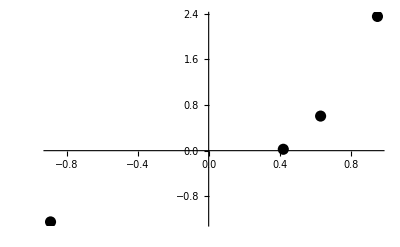
```mathematica
-Graphics-
commonTangent
```

-Graphics-

{{0.95,2.34858},{0.63,0.605016},{0.42,0.0241909},{-0.89,-1.24672}}

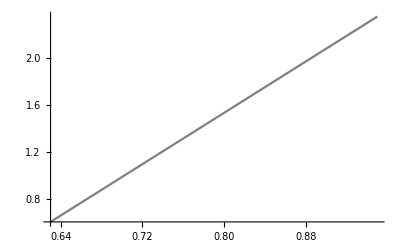

```mathematica
p11 = Plot[(2.34858 - 0.605016)/(0.95 - 0.63)*(x - 0.95) + 2.34858, {x, 0.63, 0.95}, PlotStyle -> {Gray}]
```

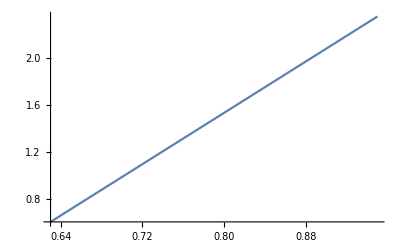
```mathematica
-Graphics-
p22 = Plot[(0.0241909 + 1.24672)/(0.42 + 0.89)*(x - 0.42) - 0.0241909, {x, -0.89, 0.42}, PlotStyle -> {Gray}]
```

-Graphics-

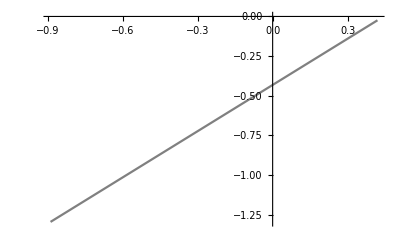

```mathematica
Show[pa, pb,p11, p22, pcc]
```

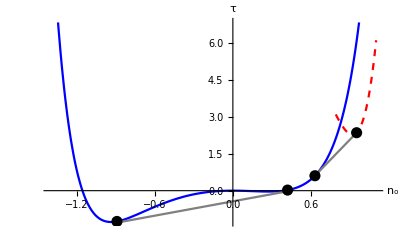

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

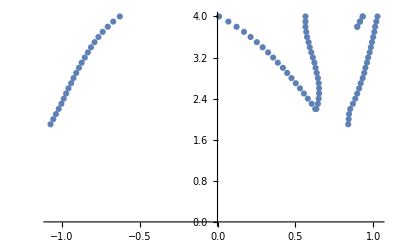

```mathematica
commonTangent = {};
spinodal = {};
convexStep = 0.0025;
For[T=1.9, T< 4.1, T = T + 0.1,  
	fcn=Table[{i,Ffcc[i, T]},{i,nmin,nmax,convexStep}]  ;
	b = Interpolation[fcn, Method-> "Spline"];
	spin = b'';
	s1=x/.FindRoot[spin[x]==0,{x,-0.7}];
	s2=x/.FindRoot[spin[x]==0,{x,0.2}];
	s3=x/.FindRoot[spin[x]==0,{x,0.7}];
	convHull = ConvexHullMesh[fcn];
	convHulln = MeshCoordinates[convHull][[All, 1]];

	len = Length[convHulln];
	dummy = {};

	For[i =  len, i>2, i--,
	If[Abs[convHulln[[i]] -(convHulln[[i - 1]] )]- convexStep>0.000001  ,
	dummy = Append[dummy, {convHulln[[i]], convHulln[[i - 1]]}]
	]
	];
	
	For[ j = 1, j <= Length[dummy], j++,
	commonTangent = Append[commonTangent, {dummy[[j,1]], T}];
	commonTangent = Append[commonTangent, {dummy[[j,2]], T}];
	];
If[T<2.0,
If[Abs[s1] > 0.0001, 
spinodal=Append[spinodal,{s1,T}];
];
If[Abs[s2] > 0.0001,
spinodal=Append[spinodal,{s2,T}];
];
If[Abs[s3] > 0.0001,
spinodal=Append[spinodal,{s3,T}];
];
];

];
ListPlot[commonTangent]
```

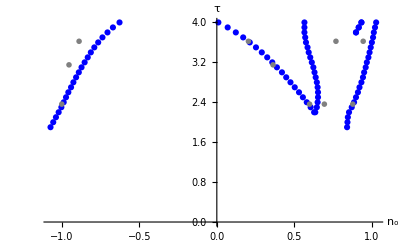

```mathematica
MenderosPRE1993 = {{0.906, 0.75},{1.004, 0.75},{0, 0.75},{0.855, 0.75},{0.025, 1},{0.729,1},{0.946, 1.15},{1.040, 1.15},{0.0598, 1.15},{0.644, 1.15},{0.966, 1.35},{1.055, 1.35},{0.1433, 1.35},{0.5087, 1.35}};


rhoBar = 0.535;
T0 = 3.15;
Do[	
	MenderosPRE1993[[i,1]] = (MenderosPRE1993[[i,1]] - rhoBar )/rhoBar;
	MenderosPRE1993[[i,2]] = MenderosPRE1993[[i,2]] *T0 ;(*fit the temperature data*),
{i, 1, Length[MenderosPRE1993]}
]
p1 = ListPlot[MenderosPRE1993,  PlotStyle->Gray, PlotMarkers -> "OpenMarkers", PlotStyle -> Gray];
p2 = ListPlot[spinodal, PlotStyle -> Orange];
p3 = ListPlot[commonTangent,  PlotStyle-> Blue, AxesLabel->{Style["n_o",Black, FontSize->15], Style["τ",Black, FontSize-> 20]}, TicksStyle->Directive[Black, 10]];
Show[ p3, p1]
```

```mathematica
cToK = 273.15;
amg = 44.615036*1/100^3;
helper=42062.75735(* this is 1/sigma^3*1/NA*);
amuArgon=39.948 (*g/mol,atomic mass of argon*);
epsil=119.8(*K*);
```

```mathematica
menderos ={{ 0.00521739130434784,0.7555555555555555},
{ 0.02608695652173909,1.0000000000000004},
{ 0.05739130434782602,1.1500000000000004},
{ 0.1460869565217391,1.35},
{ 0.5060869565217391,1.35},
{ 0.6423067632850242,1.154239540466392},
{ 0.724080112721417,1.0015260631001368},
{ 0.847369162640902,0.7550411522633742},
{ 0.9077556360708535,0.7550411522633742},
{ 0.9366908212560386,1.0015260631001368},
{ 0.9505293880837359,1.154239540466392},
{ 0.9681421095008055,1.3551783264746227},
{ 1.0524315619967792,2.753712277091907},
{ 1.1530756843800325,2.753712277091907},
{ 1.0587218196457329,1.357857510288066},
{ 1.0423671497584541,1.154239540466392},
{ 1.0310446859903384,1.0015260631001368},
{ 1.0071417069243158,0.7496827846364882}};

Do[	
	menderos [[i,1]] = menderos [[i, 1]] *helper*amuArgon* (1/(100^3));
	menderos [[i,2]] =menderos [[i,2]]*epsil,
{i, 1, Length[menderos ]}
]
```

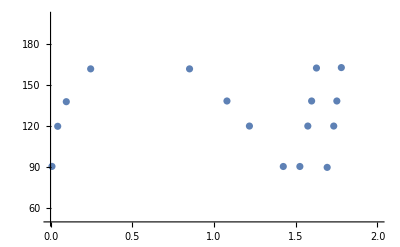

```mathematica
pMenderos = ListPlot[menderos,PlotRange->{{0, 2.0}, {50, 200}}]
```

```mathematica
michels = {{288.5, -122.3},
{312.0, -122.3},
{258.1, -122.5},
{343.3, -122.5},
{227.6, -123},
{375.1, -123},
{194.5, -124},
{410.1, -124},
{176.0, -125},
{430.7, -125},
{ 161.1, -126},
{ 448.6, -126},
{ 148.8, -127},
{463.4, -127},
{138.6, -128},
{475.9, -128},
{129.4, -129},
{487.4, -129},
{121.2, -130},
{ 498.1, -130},
{113.9, -131},
{ 508.3, -131},
{107.1, -132},
{517.8, -132},
{100.9, -133},
{526.7, -133},
{ 95.3, -134},
{ 535.0, -134},
{ 90.2, -135},
{ 542.8, -135},
{85.2, -136},
{550.6, -136},
{ 80.6, -137},
{557.7, -137},
{76.4, -138},
{564.8, -138},
{72.3, -139},
{571.6, -139},
{68.7, -140},
{578.2, -140},
{65.0, -141},
{ 584.6, -141},
{61.7, -142 },
{590.9,  -142},
{58.6,  -143},
{596.8,  -143},
{55.5, -144},
{ 602.5, -144},
{ 52.6, -145},
{ 608.2, -145},
{49.9, -146},
{ 613.7, -146},
{47.3, -147},
{619.3, -147},
{44.9, -148},
{624.6, -148},
{42.5, -149},
{629.7, -149},
{40.2, -150},
{634.8, -150},
{ 38.1, -151},
{639.7, -151},
{36.0, -152},
{644.6, -152},
{ 34.0, -153},
{649.5, -153}};
Do[	
	michels[[i,1]] = michels[[i, 1]] * amg*amuArgon;
	michels[[i,2]] = michels[[i,2]]+ cToK,
{i, 1, Length[michels]}
]
```

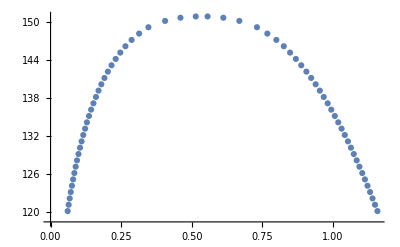

```mathematica
pMichels = ListPlot[michels]
```

```mathematica
(*Temperature (K), density (g/cm^3)*)
witzenberg = {{1.465, 96.41},
{1.640, 96.41},
{1.485, 101.11},
{1.652,101.11},
{ 1.501,105.81},
{ 1.662,105.81},
{ 1.517,110.55},
{1.673,110.55},
{ 1.532,115.30},
{ 1.682,115.30},
{ 1.547,120.08},
{ 1.691,120.08}
};
```

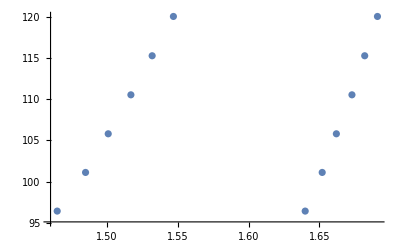

```mathematica
pWitzenberg = ListPlot[witzenberg]
```

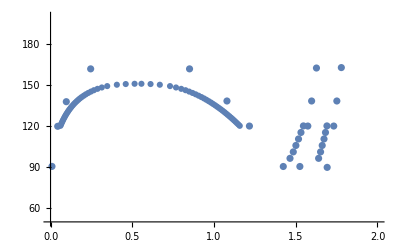

```mathematica
Show[pMenderos, pMichels, pWitzenberg]
```